(T (1+z))/(T-2 τ+T z+2 τ z)TTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`z11$CellContext`T$CellContext`T1FalseFalseFalseAutomaticNoneAutomatic

1/(1+0.05 s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

{1. ⅇ^(-20. t) (-1.+1. ⅇ^(20. t)) UnitStep[t]}

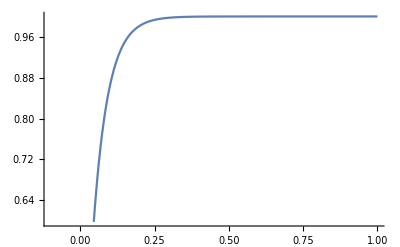

```mathematica
trans=TransferFunctionModel[1/(τ*s+1),s];
dis=ToDiscreteTimeModel[trans,T,z]
sys=trans/.τ->0.05
f=OutputResponse[sys,UnitStep[t],t]
p1=Plot[f,{t,-0.1,1}]
```

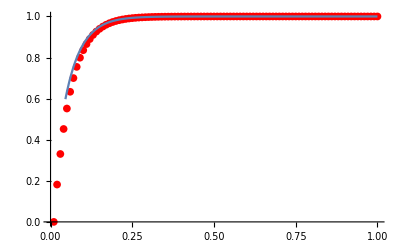

1.

```mathematica
Tick=100;
xyseries=Table[{i/Tick,0},{i,1,Tick}];
For[i=1,i<Tick,i++,
xyseries[[i+1]][[2]]=((2T)/(2τ+T)-xyseries[[i]][[2]]*(T-2τ)/(2τ+T))/.{τ->0.05,T->1/Tick}
];

p2=ListPlot[xyseries,PlotStyle->Red];
Show[p2,p1]
xyseries[[Tick]][[2]]
```